```mathematica
(*GLOBAL INITIALIZATION*)
(*Initialize kernals*)
ParallelEvaluate[$RecursionLimit=100000];
kernalIDs=ParallelEvaluate[$KernelID];

(*Position of the lost plan*)
distantR = 0.8;

(*
	The position where the plane actually is lost at
	The plane start getting missing at {0,0}
*)
θ=RandomReal[{0,2π}];
lostX = distantR*Cos[θ];
lostY = distantR*Sin[θ];
(*stepDist is the *)
stepDist=0.1;

(*Prec is the range when the object is likely to bedescivered*)
prec = stepDist/2;

(*Range*)
rangeX={-1,1};
rangeY={-1,1};
(*Minimal Probability possible*)
(*minP=1/((rangeX[[2]]-rangeX[[1]])*((rangeY[[2]]-rangeY[[1]]))/stepDist^2*10000);*)
minP=0;
(*Function that change from a position to an index*)
indexOf[x_,y_]:=Module[{},
{Round[(x-(rangeX[[1]]))/stepDist]+1,Round[(y-(rangeY[[1]]))/stepDist]+1}
];
lostIndexP=indexOf[lostX,lostY];
lostIndexX=lostIndexP[[1]];
lostIndexY=lostIndexP[[2]];

(*Whether to show the update when the searcher is searching something*)
displayDuringSearching=False;
```

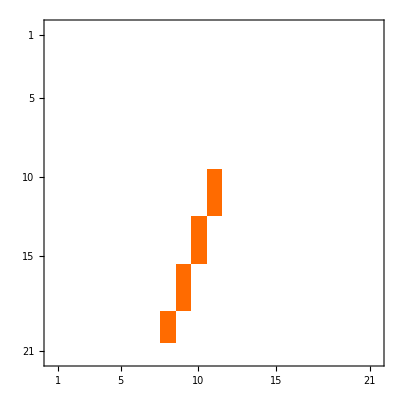
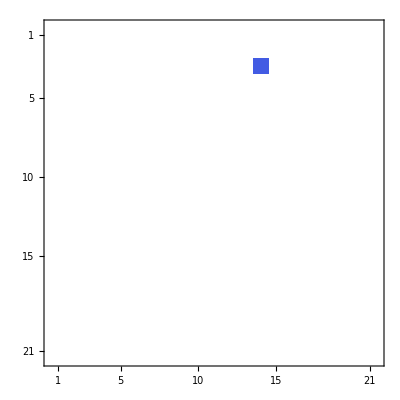
{-Graphics-,-Graphics-,{-0.754912,0.26478}}

```mathematica
(*Simulation Environment*)
(*If the position(x,y) is on the path*)
isOnPath[x_,y_]:=Module[{m=lostY/lostX, expT=prec},
(*Linear Path*)
Abs[x-0]+Abs[x-Cos[ArcTan[m]]*distantR]-1<expT && 
Abs[y-m*x] <expT
];

(*Whether the position is the plane position*)
isFound[x_,y_]:=Module[{rt = prec,lp,lx,ly},
lp=indexOf[x,y];
lx=lp[[1]];
ly=lp[[2]];
lostIndexX==lx && lostIndexY==ly
];

(* The probability that we give evidence when searching at the path*)
pEvidenceFoundOnPath=0.3;

(*Search a particular Point in the map*)
searchMapAtPoint[x_,y_]:=Module[{p=RandomReal[{0,1}] < pEvidenceFoundOnPath},
isOnPath[x,y] && p
];

(*Update the Data At Specific Point*)
changeDataAt[list_,posX_,posY_,newValue_]:=Parallelize[Table[
If[
Abs[posX-x]< prec &&Abs[posY-y]<prec,
newValue,
list[[
indexOf[x,y][[1]]
]][[
indexOf[x,y][[2]]
]]
],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
]
];

(*Initialize experiment Environment*)
generateLostPoint[r_,theta_,step_,range_]:=Module[{},
(*Position of the lost plan*)
distantR = r;

(*
	The position where the plane actually is lost at
	The plane start getting missing at {0,0}
*)
θ=theta;
{lostX,lostY}={distantR*Cos[θ],distantR*Sin[θ]};

{lostIndexX,lostIndexY}=lostIndexP=indexOf[lostX,lostY];

(*stepDist is the *)
stepDist=step;

(*Prec is the range when the object is likely to bedescivered*)
prec = stepDist/2;

(*Range*)
{rangeX,rangeY}=range;
];

plotPlaneInformation[]:=Module[{},
(*Plot lost point*)
planePathData = Parallelize[Table[If[isOnPath[x,y],1,0],{x,-1,1,stepDist},{y,-1,1,stepDist}]];
plotLostPlane =Parallelize[Table[0,{x,-1,1,stepDist},{y,-1,1,stepDist}]];
plotLostPlane= changeDataAt[plotLostPlane,lostX,lostY,-100];

Print[{
(*ListDensityPlot[planePathData,PlotRange->All],
ListDensityPlot[data,PlotRange->All],*)
MatrixPlot[planePathData,PlotRange->All],
MatrixPlot[plotLostPlane,PlotRange->All],
{lostX,lostY}
}];
];
plotPlaneInformation[];
```

```mathematica
(* 
  searcher data is the probability density of the 
	probability that the searcher can find the object
	given that the object is in the position
	P(D|O)
data is the probability density of the 
	probability that if the object is in the position
	and given that we can detected it
	P(D|O)*P(O)=P(O|D)
*)
searcherModel[objectData_,searcherData_]:=Module[{
data,

getSearchPoint,
searchPoint,
plotData,
max=-Infinity,
x=rangeX[[1]], y=rangeY[[1]],
mx=0,my=0,ix,iy
},

data=objectData*searcherData;

(* Found the next search point *)
While[x-rangeX[[2]] < prec,
While[y-rangeY[[2]] < prec,
{ix,iy}=indexOf[x,y];
If[
max<data[[ix]][[iy]],
max=data[[ix]][[iy]];
mx=x;
my=y;
(*Print[{max,list[[ix]][[iy]], {ix,iy},{x,y},{px,py}}]*);
];
y+=stepDist;
];
y=rangeY[[1]];
x+=stepDist;
];

searchPoint ={mx,my};
(*plotData= changeDataAt[data,mx,my,-1];*)
If[displayDuringSearching,
Print[{MatrixPlot[data],MatrixPlot[objectData],MatrixPlot[searcherData],MatrixPlot[plotData]}];
Print[{
ListPointPlot3D[data,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[-z]]],
ListPointPlot3D[objectData,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[-z]]],
ListPointPlot3D[searcherData,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[-z]]],
(*ListPlot3D[plotData,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[z]]]*)
}
];
];

Return[
<|
"ret"->Apply[isFound,searchPoint],
"pos"->searchPoint,
"posIndex"->Apply[indexOf,searchPoint],
"pdo"-> searcherData[[Apply[indexOf,searchPoint][[1]]]][[Apply[indexOf,searchPoint][[2]]]],
"poo"-> data[[Apply[indexOf,searchPoint][[1]]]][[Apply[indexOf,searchPoint][[2]]]],
"pdData"-> <|
"matrix"-> data,
"sum"->  Total[Flatten[data]]
 |>
|>
];
];
```

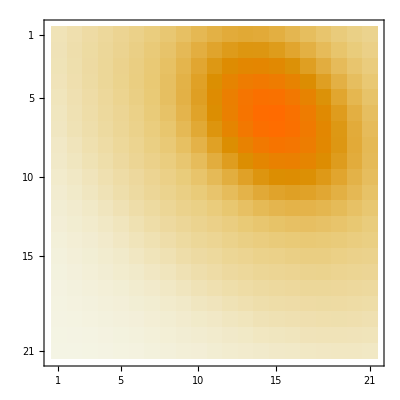
{-Graphics3D-,-Graphics-}

```mathematica
(* Object Data *)
(* precondition:  0<ρ<1 *)
objectDataInit[ρ_:0.3,σx_:0.3,σy_:0.3,γ_:0.2]:=Module[{centerX,centerY},
centerX=lostX*0.8+γ*RandomReal[]*distantR;
 centerY=lostY*0.8+γ*RandomReal[]*distantR;
Function[{x,y},PDF[MultinormalDistribution[{centerX,centerY},{{σx^2,ρ*σx*σy},{ρ*σx*σy,σy^2}}],{x,y}]*stepDist^2]
];

(*Update ObjectData*)
updateObjectData[f_]:=Module[{},
objectData=Parallelize[
Table[f[x,y],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
]]
];

(* has to manually initialize *)
tmpf=objectDataInit[];
updateObjectData[tmpf];

Print[{
DiscretePlot3D[tmpf[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist},ExtentSize->stepDist],
MatrixPlot[objectData]
}];
```

```mathematica
(*FUnction that display data pdf*)
printDataPDF[pdf_]:=Module[{tmp},
tmp=Parallelize[Table[pdf[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist}]];
Print[{
DiscretePlot3D[pdf[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist},ExtentSize->stepDist],
MatrixPlot[tmp],
(*tmp*)
}];
];
```

```mathematica
(* {cx,cy} is the initial center of the searcher *)
(* precondition:  0<ρ<1 *)
generateSearcherData[centerX_,centerY_,a_,bx_,by_]:=Module[
{},
Function[{x,y},PDF[MultinormalDistribution[{centerX,centerY},{{bx^2,a*bx*by},{a*bx*by,by^2}}],{x,y}]*stepDist^2*50]
];

searchers={};

(* 
Generate Searchers of a specific functions for multiple times(allowed different configurations);
	para;
		num=>number of searchesr;
		fun: function of the pdf*area;
		parameters: a list of parameters for each function, could be the same or different
*)
generateSearchers[funs_]:=Module[{},
searchers= Parallelize[Map[
Function[f,Table[
f[x,y],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
]],funs]
]
];

initSearcherFunctions[maxT_]:=Module[{initList={},i},
For[i=0,i<maxT,i++,initList=Append[initList,1]];
Parallelize[Map[Function[para,Apply[generateSearcherData,para]],
Map[Function[a,Map[Function[x,RandomReal[x]],{{-1,1},{-1,1},{-1,1},{0,1},{0,1}}]],initList]
]]
];
generateSearchers[initSearcherFunctions[5]];
```

```mathematica
(*ret=searcherModel[objectData,searchers[[1]]];
MatrixPlot[ret[pdData][matrix]];
ret[pdData][sum];*)
```

```mathematica
(* Let a list of searchers to search with a particular condition *)
allSearch[searchers_,objectData_]:=
WaitAll[ParallelSubmit[Map[Function[sd,searcherModel[objectData,sd]],searchers]]];

(*searchResults=allSearch[searchers,objectData];*)
```

```mathematica
(* Incorproate the search result to generate a new update*)

(* test whether the search is successful *)
isSuccessful[result_]:=Fold[Or,False,Parallelize[Map[Function[a,a["ret"]],result]]];
```

```mathematica
(*Flatter the list so that I know what are the position that the searcher searched*)
restracture[result_]:=
Parallelize[Map[Function[a,{a["posIndex"],a["poo"]*a["pdo"],a["poo"]*(1-a["pdo"])}],result]];
```

```mathematica
calculateDenominator[restruct_]:=Fold[Function[{x,y},x-y],1,restruct][[2]];
```

```mathematica
reduceColumneProduct[restruct_,denominator_]:=Parallelize[Map[Function[x,{x[[1]],x[[3]]/denominator}],restruct]];
```

```mathematica
(* Function to check whether contains *)
restructContains[result_,{px_,py_}]:=Fold[
Function[{prev,current},
prev || current[[1]] == {px,py}
],False,result];
```

```mathematica
(*
Extract result from the structure 
TODO! should I make it return ZERO? which is safer?
*)
extractRestruct[result_,{px_,py_}]:=
Fold[Function[{prev,current},
If[prev==-Infinity &&current[[1]] == {px,py},current[[2]],prev]
],-Infinity,result];
```

```mathematica
(* Generate a new List *)
updateObjectProbabilityAfterFail[result_,denominator_,originalObjectData_ ]:=Module[{tmp,f},
f[x_,y_]:=Module[{pos},
pos=indexOf[x,y];
If[
restructContains[result,pos],
extractRestruct[result,pos],
originalObjectData[[pos[[1]]]][[pos[[2]]]]/denominator
 ]
];
Parallelize[Table[f[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist}]]
];
```

```mathematica
(*Main Searcher Algorithm*)
(*
	1. po(plot);
	2. search plot;
	3. pd=po*pdo sum
*)
multiSearcherSearch[initObjectData_,searchers_,max_,logInterval_]:=Module[
{data=initObjectData,searchResults,
temp,originalData,restruct,denominator,restructSearchRet,t,
diff=initObjectData,logData={},logPresent},

Print["Search Begin!"];
Monitor[
t=0;
While[t==0||!isSuccessful[searchResults] && t<max,
originalData=data;
(*Print[MatrixPlot[originalData]];*)

(*get the search result*)
searchResults=allSearch[searchers,originalData];
(*Print[MatrixForm[searchResults]];*)

restructSearchRet=restracture[searchResults];
(*Print[restructSearchRet];*)

denominator=calculateDenominator[restructSearchRet];
(*Print[denominator];*)

restruct=reduceColumneProduct[restructSearchRet,denominator];
(*Print[restruct];*)

data=updateObjectProbabilityAfterFail[restruct,denominator, originalData];
diff =originalData-data;

If[Mod[t,logInterval]==0,Module[{},
logPresent=
<|
"time"-> t,
"poPlot"-> {MatrixPlot[data],ListPlot3D[data,PlotRange->All]},
"poData"-> data,
"sr"-> searchResults
|>;
(*Print[logPresent];*)
logData=Append[logData,logPresent];
]];

t++;
];
,{MatrixPlot[originalData],MatrixPlot[data],MatrixPlot[diff],ListContourPlot[data],t}];

Print[{MatrixPlot[initObjectData],MatrixPlot[data], MatrixPlot[initObjectData-data],t}];
Print[{
ListContourPlot[initObjectData,InterpolationOrder->3,PlotLegends->Automatic],ListContourPlot[data,InterpolationOrder->3,PlotLegends->Automatic],
 ListContourPlot[initObjectData-data,InterpolationOrder->3,PlotLegends->Automatic],t}];
Print[{ListPlot3D[initObjectData,PlotRange->All], ListPlot3D[data,PlotRange->All],ListPlot3D[initObjectData-data,PlotRange->All]}];
(*Print[MatrixForm[searchResults]];*)
logData
];
```

```mathematica
(*
1. generate your P(O) distribution,each will be a function to plug into updateObjectData[f]
original function will be object data init, which is a binoral distribution centered at the place where the plane is lost
*)
(*updateObjectData[objectDataInit];*)

(*
2. generate your searchers!(each one is a PDF that can be put into≥
*)

(*multiSearcherSearch[objectData,searchers,50,5];*)
```

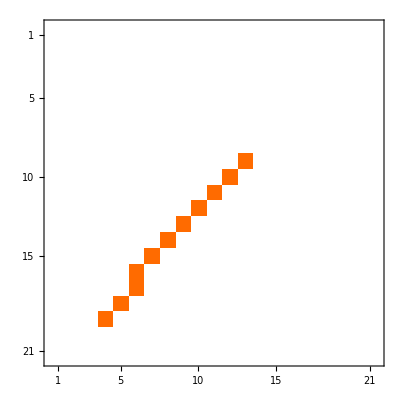
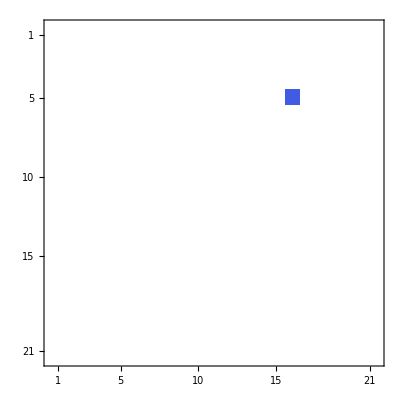
{-Graphics-,-Graphics-,{-0.591146,0.539024}}

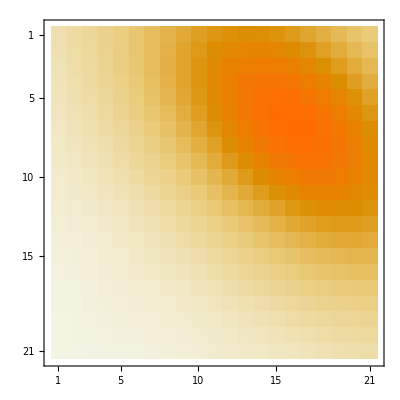
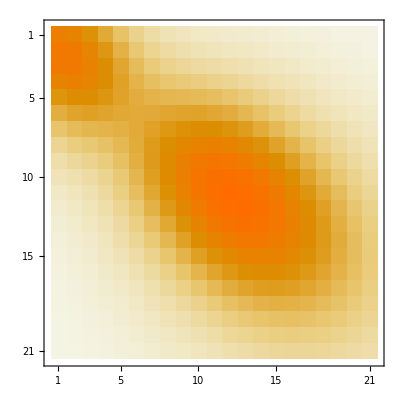
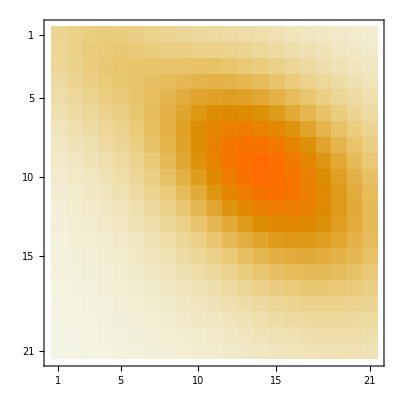
{{-Graphics-,-Graphics3D-},{-Graphics-,-Graphics3D-},{-Graphics-,-Graphics3D-}}

Search Begin!

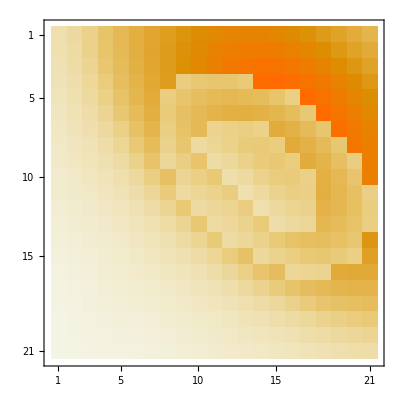
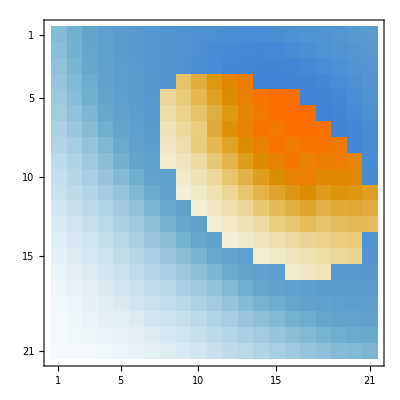
{-Graphics-,-Graphics-,-Graphics-,161}

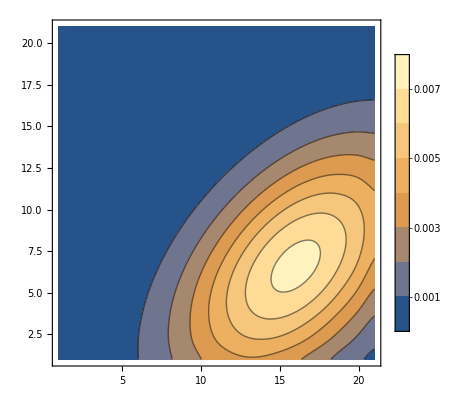
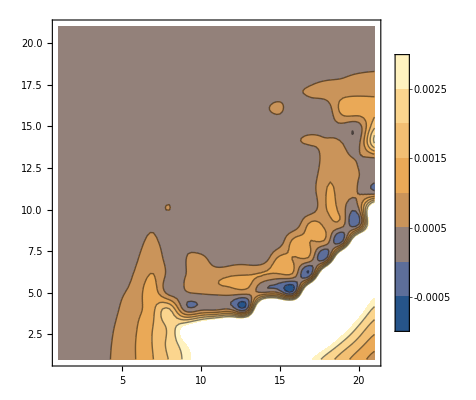
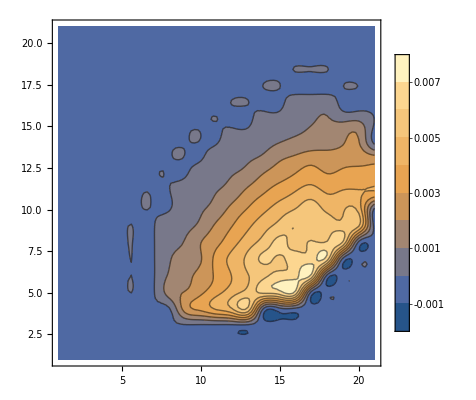
{-Graphics-,-Graphics-,-Graphics-,161}

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*
	1. Single searcher;
	2. 20*20= 400 areas; step=0.05
	3. PO = multinormal distribution;
	3. PDO = bimodal multivariable possoin distribution
*)
SimulationOne[]:=Module[{searchers,objectData,pdo,𝒟,f,prod},
(*initialize the environment*)
generateLostPoint[0.8,RandomReal[{0,π}],0.1,{{-1,1},{-1,1}}];
plotPlaneInformation[];

f=objectDataInit[0.5,0.5,0.5];
objectData=updateObjectData[f];


𝒟=MixtureDistribution[{3,1},{MultivariatePoissonDistribution[7,{9,10}],MultivariatePoissonDistribution[2,{5,4}]}];
searchers={Parallelize[Table[100*PDF[𝒟,{x,y}],
{x,5,25},
{y,5,25}
]]};
Print[{
{MatrixPlot[objectData],ListPlot3D[objectData,PlotRange->All]},
{MatrixPlot[searchers[[1]]], ListPlot3D[searchers[[1]],PlotRange-> All]},
{MatrixPlot[searchers[[1]]*objectData], ListPlot3D[searchers[[1]]*objectData,PlotRange-> All]}
}];

multiSearcherSearch[objectData,searchers,Infinity,5]
];
simulationData=SimulationOne[];
```

0

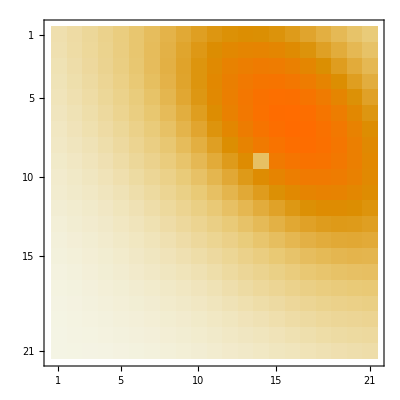
{-Graphics-,-Graphics3D-}

ListContourPlot::arrayerr: Missing["KeyAbsent", "poData"] must be a valid array.

ListContourPlot[Missing[KeyAbsent,poData]]

False

{-0.2,0.3}

{9,14}

-Graphics-

0.1447

{<|ret→False,pos→{-0.2,0.3},posIndex→{9,14},pdo→100 (3745213911044282711525/(3708782453376 ⅇ^26)+1394765270148608/(23763009449804625 ⅇ^11)),poo→0.00257065,pdData→<|matrix→{{0.0000421716,0.0000715818,0.0000974753,0.00010919,0.000103109,0.0000846315,0.0000632142,0.00004589,0.0000345346,0.0000273763,0.00002192,0.0000167733,0.0000118236,7.54613×10^-6,4.33383×10^-6,2.23747×10^-6,1.03955×10^-6,4.35434×10^-7,1.64765×10^-7,5.64324×10^-8,1.75281×10^-8},{0.0000421299,0.0000778207,0.00011529,0.000140747,0.000145743,0.00013311,0.00011359,0.0000971066,0.0000868365,0.0000798079,0.0000714637,0.0000595714,0.0000450987,0.0000306978,0.0000187378,0.0000102619,5.05112×10^-6,2.2393×10^-6,8.96053×10^-7,3.24299×10^-7,1.06362×10^-7},{0.0000337074,0.000067689,0.000109137,0.000145621,0.000166594,0.000171764,0.000170677,0.000173664,0.000182897,0.000191239,0.00018867,0.000169942,0.000137658,0.0000997774,0.0000646902,0.0000375734,0.0000195929,9.19375×10^-6,3.89078×10^-6,1.48816×10^-6,5.1545×10^-7},{0.0000220851,0.0000481938,0.000084698,0.00012417,0.000158755,0.000188182,0.000221369,0.000267962,0.000326698,0.000381569,0.000410013,0.000396807,0.000343053,0.000264494,0.000182066,0.000112134,0.0000619448,0.0000307671,0.0000137717,5.56729×10^-6,2.03671×10^-6},{0.0000120609,0.000028616,0.0000550101,0.0000893917,0.000129797,0.000180335,0.000253163,0.000360179,0.000498158,0.000640067,0.000742952,0.000769573,0.000708873,0.000580928,0.000424428,0.000277157,0.000162191,0.0000852719,0.0000403727,0.0000172515,6.66656×10^-6},{5.57184×10^-6,0.0000144052,0.0000304896,0.0000556605,0.0000935924,0.000154665,0.000257935,0.000422929,0.000651211,0.000909984,0.0011345,0.00125448,0.00122972,0.00107059,0.000829962,0.000574565,0.00035617,0.000198213,0.0000992683,0.0000448387,0.0000183043},{2.20684×10^-6,6.2468×10^-6,0.0000147164,0.0000307323,0.0000609718,0.000120289,0.000234529,0.000433854,0.000732587,0.00110438,0.00147316,0.0017358,0.00180922,0.00167256,0.00137553,0.00100938,0.000662768,0.000390414,0.000206824,0.0000987559,0.0000425904},{7.59321×10^-7,2.37368×10^-6,6.32423×10^-6,0.0000154167,0.000036488,0.0000850966,0.000189782,0.000388777,0.000712046,0.00115166,0.0016394,0.00205576,0.00227682,0.00223425,0.00194885,0.00151567,0.00105404,0.000657182,0.000368259,0.000185882,0.0000846934},{2.30249×10^-7,8.05816×10^-7,2.47719×10^-6,7.1655×10^-6,0.0000201835,0.0000545474,0.000136188,0.00030457,0.000600483,0.00103818,0.00157424,0.00209888,0.00246874,0.00257065,0.00237763,0.00195948,0.00144308,0.00095225,0.000564403,0.000301156,0.000144967},{6.25747×10^-8,2.49815×10^-7,9.03621×10^-7,3.11734×10^-6,0.0000102879,0.0000314834,0.0000864588,0.000208978,0.000441283,0.000813487,0.00131227,0.00185887,0.00232092,0.00256358,0.00251359,0.00219472,0.00171145,0.00119512,0.00074919,0.000422564,0.000214896},{1.55497×10^-8,7.23138×10^-8,3.11332×10^-7,1.26862×10^-6,4.79421×10^-6,0.0000162729,0.000048526,0.000125912,0.000283801,0.000556862,0.000954689,0.00143589,0.00190224,0.00222805,0.00231529,0.00214134,0.0017678,0.0013062,0.000865945,0.000516251,0.000277357},{3.61177×10^-9,1.98877×10^-8,1.01614×10^-7,4.79015×10^-7,2.02583×10^-6,7.50719×10^-6,0.0000240969,0.0000668205,0.000160391,0.000334544,0.000609061,0.0009721,0.00136584,0.00169582,0.0018671,0.0018287,0.00159797,0.00124913,0.00087566,0.000551743,0.000313135},{7.99669×10^-10,5.2331×10^-9,3.12001×10^-8,1.66098×10^-7,7.71543×10^-7,3.08726×10^-6,0.0000106052,0.0000313345,0.0000799652,0.000177125,0.0003422,0.000579282,0.000862853,0.00113523,0.00132387,0.00137278,0.00126943,0.00104963,0.00077794,0.000517999,0.000310529},{1.70634×10^-10,1.31154×10^-9,8.90881×10^-9,5.24331×10^-8,2.63938×10^-7,1.1321×10^-6,4.1461×10^-6,0.0000130257,0.0000352984,0.0000829619,0.00016998,0.000305032,0.000481462,0.000670984,0.000828526,0.000909325,0.00088963,0.000777916,0.000609472,0.000428804,0.000271497},{3.50476×10^-11,3.09425×10^-10,2.33967×10^-9,1.4983×10^-8,8.09999×10^-8,3.70655×10^-7,1.44353×10^-6,4.81504×10^-6,0.0000138421,0.0000344947,0.0000749092,0.00014243,0.000238121,0.000351383,0.00045926,0.000533335,0.000551895,0.000510246,0.000422502,0.000314042,0.000209976},{6.85471×10^-12,6.78396×10^-11,5.60628×10^-10,3.86417×10^-9,2.23047×10^-8,1.0855×10^-7,4.48757×10^-7,1.58744×10^-6,4.83714×10^-6,0.0000127726,0.0000293817,0.0000591624,0.000104719,0.000163557,0.00022619,0.000277847,0.000304023,0.000297113,0.000259961,0.0002041,0.000144091},{1.25869×10^-12,1.36803×10^-11,1.21985×10^-10,8.9859×10^-10,5.51715×10^-9,2.84952×10^-8,1.24883×10^-7,4.68059×10^-7,1.51064×10^-6,4.22392×10^-6,0.000010287,0.0000219252,0.0000410684,0.0000678628,0.0000992669,0.000128938,0.000149141,0.000154025,0.000142369,0.000118043,0.0000879776},{2.14327×10^-13,2.52054×10^-12,2.4048×10^-11,1.88469×10^-10,1.22777×10^-9,6.71958×10^-9,3.11869×10^-8,1.23745×10^-7,4.22729×10^-7,1.2509×10^-6,3.22357×10^-6,7.26868×10^-6,0.0000144015,0.0000251668,0.0000389225,0.0000534404,0.0000653228,0.0000712717,0.0000695776,0.0000609103,0.000047916},{3.35526×10^-14,4.22773×10^-13,4.29279×10^-12,3.5689×10^-11,2.46253×10^-10,1.4265×10^-9,7.00524×10^-9,2.94053×10^-8,1.06256×10^-7,3.32558×10^-7,9.06329×10^-7,2.161×10^-6,4.52678×10^-6,8.36224×10^-6,0.0000136686,0.0000198303,0.0000256072,0.0000295083,0.0000304167,0.0000281078,0.0000233338},{4.80468×10^-15,6.44591×10^-14,6.94188×10^-13,6.11006×10^-12,4.45975×10^-11,2.73187×10^-10,1.41841×10^-9,6.29447×10^-9,2.40447×10^-8,7.95494×10^-8,2.29154×10^-7,5.77468×10^-7,1.27834×10^-6,2.49518×10^-6,4.3088×10^-6,6.60296×10^-6,9.00452×10^-6,0.0000109557,0.0000119207,0.0000116253,0.000010182},{6.27778×10^-16,8.93189×10^-15,1.01793×10^-13,9.47218×10^-13,7.3063×10^-12,4.72889×10^-11,2.59412×10^-10,1.21627×10^-9,4.90866×10^-9,1.71571×10^-8,5.2213×10^-8,1.38994×10^-7,3.25007×10^-7,6.7001×10^-7,1.22183×10^-6,1.977×10^-6,2.84621×10^-6,3.65512×10^-6,4.19694×10^-6,4.31826×10^-6,3.98943×10^-6}},sum→0.1447|>|>}⟦2⟧[ret]

{<|ret→False,pos→{-0.2,0.3},posIndex→{9,14},pdo→100 (3745213911044282711525/(3708782453376 ⅇ^26)+1394765270148608/(23763009449804625 ⅇ^11)),poo→0.00257065,pdData→<|matrix→{{0.0000421716,0.0000715818,0.0000974753,0.00010919,0.000103109,0.0000846315,0.0000632142,0.00004589,0.0000345346,0.0000273763,0.00002192,0.0000167733,0.0000118236,7.54613×10^-6,4.33383×10^-6,2.23747×10^-6,1.03955×10^-6,4.35434×10^-7,1.64765×10^-7,5.64324×10^-8,1.75281×10^-8},{0.0000421299,0.0000778207,0.00011529,0.000140747,0.000145743,0.00013311,0.00011359,0.0000971066,0.0000868365,0.0000798079,0.0000714637,0.0000595714,0.0000450987,0.0000306978,0.0000187378,0.0000102619,5.05112×10^-6,2.2393×10^-6,8.96053×10^-7,3.24299×10^-7,1.06362×10^-7},{0.0000337074,0.000067689,0.000109137,0.000145621,0.000166594,0.000171764,0.000170677,0.000173664,0.000182897,0.000191239,0.00018867,0.000169942,0.000137658,0.0000997774,0.0000646902,0.0000375734,0.0000195929,9.19375×10^-6,3.89078×10^-6,1.48816×10^-6,5.1545×10^-7},{0.0000220851,0.0000481938,0.000084698,0.00012417,0.000158755,0.000188182,0.000221369,0.000267962,0.000326698,0.000381569,0.000410013,0.000396807,0.000343053,0.000264494,0.000182066,0.000112134,0.0000619448,0.0000307671,0.0000137717,5.56729×10^-6,2.03671×10^-6},{0.0000120609,0.000028616,0.0000550101,0.0000893917,0.000129797,0.000180335,0.000253163,0.000360179,0.000498158,0.000640067,0.000742952,0.000769573,0.000708873,0.000580928,0.000424428,0.000277157,0.000162191,0.0000852719,0.0000403727,0.0000172515,6.66656×10^-6},{5.57184×10^-6,0.0000144052,0.0000304896,0.0000556605,0.0000935924,0.000154665,0.000257935,0.000422929,0.000651211,0.000909984,0.0011345,0.00125448,0.00122972,0.00107059,0.000829962,0.000574565,0.00035617,0.000198213,0.0000992683,0.0000448387,0.0000183043},{2.20684×10^-6,6.2468×10^-6,0.0000147164,0.0000307323,0.0000609718,0.000120289,0.000234529,0.000433854,0.000732587,0.00110438,0.00147316,0.0017358,0.00180922,0.00167256,0.00137553,0.00100938,0.000662768,0.000390414,0.000206824,0.0000987559,0.0000425904},{7.59321×10^-7,2.37368×10^-6,6.32423×10^-6,0.0000154167,0.000036488,0.0000850966,0.000189782,0.000388777,0.000712046,0.00115166,0.0016394,0.00205576,0.00227682,0.00223425,0.00194885,0.00151567,0.00105404,0.000657182,0.000368259,0.000185882,0.0000846934},{2.30249×10^-7,8.05816×10^-7,2.47719×10^-6,7.1655×10^-6,0.0000201835,0.0000545474,0.000136188,0.00030457,0.000600483,0.00103818,0.00157424,0.00209888,0.00246874,0.00257065,0.00237763,0.00195948,0.00144308,0.00095225,0.000564403,0.000301156,0.000144967},{6.25747×10^-8,2.49815×10^-7,9.03621×10^-7,3.11734×10^-6,0.0000102879,0.0000314834,0.0000864588,0.000208978,0.000441283,0.000813487,0.00131227,0.00185887,0.00232092,0.00256358,0.00251359,0.00219472,0.00171145,0.00119512,0.00074919,0.000422564,0.000214896},{1.55497×10^-8,7.23138×10^-8,3.11332×10^-7,1.26862×10^-6,4.79421×10^-6,0.0000162729,0.000048526,0.000125912,0.000283801,0.000556862,0.000954689,0.00143589,0.00190224,0.00222805,0.00231529,0.00214134,0.0017678,0.0013062,0.000865945,0.000516251,0.000277357},{3.61177×10^-9,1.98877×10^-8,1.01614×10^-7,4.79015×10^-7,2.02583×10^-6,7.50719×10^-6,0.0000240969,0.0000668205,0.000160391,0.000334544,0.000609061,0.0009721,0.00136584,0.00169582,0.0018671,0.0018287,0.00159797,0.00124913,0.00087566,0.000551743,0.000313135},{7.99669×10^-10,5.2331×10^-9,3.12001×10^-8,1.66098×10^-7,7.71543×10^-7,3.08726×10^-6,0.0000106052,0.0000313345,0.0000799652,0.000177125,0.0003422,0.000579282,0.000862853,0.00113523,0.00132387,0.00137278,0.00126943,0.00104963,0.00077794,0.000517999,0.000310529},{1.70634×10^-10,1.31154×10^-9,8.90881×10^-9,5.24331×10^-8,2.63938×10^-7,1.1321×10^-6,4.1461×10^-6,0.0000130257,0.0000352984,0.0000829619,0.00016998,0.000305032,0.000481462,0.000670984,0.000828526,0.000909325,0.00088963,0.000777916,0.000609472,0.000428804,0.000271497},{3.50476×10^-11,3.09425×10^-10,2.33967×10^-9,1.4983×10^-8,8.09999×10^-8,3.70655×10^-7,1.44353×10^-6,4.81504×10^-6,0.0000138421,0.0000344947,0.0000749092,0.00014243,0.000238121,0.000351383,0.00045926,0.000533335,0.000551895,0.000510246,0.000422502,0.000314042,0.000209976},{6.85471×10^-12,6.78396×10^-11,5.60628×10^-10,3.86417×10^-9,2.23047×10^-8,1.0855×10^-7,4.48757×10^-7,1.58744×10^-6,4.83714×10^-6,0.0000127726,0.0000293817,0.0000591624,0.000104719,0.000163557,0.00022619,0.000277847,0.000304023,0.000297113,0.000259961,0.0002041,0.000144091},{1.25869×10^-12,1.36803×10^-11,1.21985×10^-10,8.9859×10^-10,5.51715×10^-9,2.84952×10^-8,1.24883×10^-7,4.68059×10^-7,1.51064×10^-6,4.22392×10^-6,0.000010287,0.0000219252,0.0000410684,0.0000678628,0.0000992669,0.000128938,0.000149141,0.000154025,0.000142369,0.000118043,0.0000879776},{2.14327×10^-13,2.52054×10^-12,2.4048×10^-11,1.88469×10^-10,1.22777×10^-9,6.71958×10^-9,3.11869×10^-8,1.23745×10^-7,4.22729×10^-7,1.2509×10^-6,3.22357×10^-6,7.26868×10^-6,0.0000144015,0.0000251668,0.0000389225,0.0000534404,0.0000653228,0.0000712717,0.0000695776,0.0000609103,0.000047916},{3.35526×10^-14,4.22773×10^-13,4.29279×10^-12,3.5689×10^-11,2.46253×10^-10,1.4265×10^-9,7.00524×10^-9,2.94053×10^-8,1.06256×10^-7,3.32558×10^-7,9.06329×10^-7,2.161×10^-6,4.52678×10^-6,8.36224×10^-6,0.0000136686,0.0000198303,0.0000256072,0.0000295083,0.0000304167,0.0000281078,0.0000233338},{4.80468×10^-15,6.44591×10^-14,6.94188×10^-13,6.11006×10^-12,4.45975×10^-11,2.73187×10^-10,1.41841×10^-9,6.29447×10^-9,2.40447×10^-8,7.95494×10^-8,2.29154×10^-7,5.77468×10^-7,1.27834×10^-6,2.49518×10^-6,4.3088×10^-6,6.60296×10^-6,9.00452×10^-6,0.0000109557,0.0000119207,0.0000116253,0.000010182},{6.27778×10^-16,8.93189×10^-15,1.01793×10^-13,9.47218×10^-13,7.3063×10^-12,4.72889×10^-11,2.59412×10^-10,1.21627×10^-9,4.90866×10^-9,1.71571×10^-8,5.2213×10^-8,1.38994×10^-7,3.25007×10^-7,6.7001×10^-7,1.22183×10^-6,1.977×10^-6,2.84621×10^-6,3.65512×10^-6,4.19694×10^-6,4.31826×10^-6,3.98943×10^-6}},sum→0.1447|>|>}⟦2⟧[pos]

{<|ret→False,pos→{-0.2,0.3},posIndex→{9,14},pdo→100 (3745213911044282711525/(3708782453376 ⅇ^26)+1394765270148608/(23763009449804625 ⅇ^11)),poo→0.00257065,pdData→<|matrix→{{0.0000421716,0.0000715818,0.0000974753,0.00010919,0.000103109,0.0000846315,0.0000632142,0.00004589,0.0000345346,0.0000273763,0.00002192,0.0000167733,0.0000118236,7.54613×10^-6,4.33383×10^-6,2.23747×10^-6,1.03955×10^-6,4.35434×10^-7,1.64765×10^-7,5.64324×10^-8,1.75281×10^-8},{0.0000421299,0.0000778207,0.00011529,0.000140747,0.000145743,0.00013311,0.00011359,0.0000971066,0.0000868365,0.0000798079,0.0000714637,0.0000595714,0.0000450987,0.0000306978,0.0000187378,0.0000102619,5.05112×10^-6,2.2393×10^-6,8.96053×10^-7,3.24299×10^-7,1.06362×10^-7},{0.0000337074,0.000067689,0.000109137,0.000145621,0.000166594,0.000171764,0.000170677,0.000173664,0.000182897,0.000191239,0.00018867,0.000169942,0.000137658,0.0000997774,0.0000646902,0.0000375734,0.0000195929,9.19375×10^-6,3.89078×10^-6,1.48816×10^-6,5.1545×10^-7},{0.0000220851,0.0000481938,0.000084698,0.00012417,0.000158755,0.000188182,0.000221369,0.000267962,0.000326698,0.000381569,0.000410013,0.000396807,0.000343053,0.000264494,0.000182066,0.000112134,0.0000619448,0.0000307671,0.0000137717,5.56729×10^-6,2.03671×10^-6},{0.0000120609,0.000028616,0.0000550101,0.0000893917,0.000129797,0.000180335,0.000253163,0.000360179,0.000498158,0.000640067,0.000742952,0.000769573,0.000708873,0.000580928,0.000424428,0.000277157,0.000162191,0.0000852719,0.0000403727,0.0000172515,6.66656×10^-6},{5.57184×10^-6,0.0000144052,0.0000304896,0.0000556605,0.0000935924,0.000154665,0.000257935,0.000422929,0.000651211,0.000909984,0.0011345,0.00125448,0.00122972,0.00107059,0.000829962,0.000574565,0.00035617,0.000198213,0.0000992683,0.0000448387,0.0000183043},{2.20684×10^-6,6.2468×10^-6,0.0000147164,0.0000307323,0.0000609718,0.000120289,0.000234529,0.000433854,0.000732587,0.00110438,0.00147316,0.0017358,0.00180922,0.00167256,0.00137553,0.00100938,0.000662768,0.000390414,0.000206824,0.0000987559,0.0000425904},{7.59321×10^-7,2.37368×10^-6,6.32423×10^-6,0.0000154167,0.000036488,0.0000850966,0.000189782,0.000388777,0.000712046,0.00115166,0.0016394,0.00205576,0.00227682,0.00223425,0.00194885,0.00151567,0.00105404,0.000657182,0.000368259,0.000185882,0.0000846934},{2.30249×10^-7,8.05816×10^-7,2.47719×10^-6,7.1655×10^-6,0.0000201835,0.0000545474,0.000136188,0.00030457,0.000600483,0.00103818,0.00157424,0.00209888,0.00246874,0.00257065,0.00237763,0.00195948,0.00144308,0.00095225,0.000564403,0.000301156,0.000144967},{6.25747×10^-8,2.49815×10^-7,9.03621×10^-7,3.11734×10^-6,0.0000102879,0.0000314834,0.0000864588,0.000208978,0.000441283,0.000813487,0.00131227,0.00185887,0.00232092,0.00256358,0.00251359,0.00219472,0.00171145,0.00119512,0.00074919,0.000422564,0.000214896},{1.55497×10^-8,7.23138×10^-8,3.11332×10^-7,1.26862×10^-6,4.79421×10^-6,0.0000162729,0.000048526,0.000125912,0.000283801,0.000556862,0.000954689,0.00143589,0.00190224,0.00222805,0.00231529,0.00214134,0.0017678,0.0013062,0.000865945,0.000516251,0.000277357},{3.61177×10^-9,1.98877×10^-8,1.01614×10^-7,4.79015×10^-7,2.02583×10^-6,7.50719×10^-6,0.0000240969,0.0000668205,0.000160391,0.000334544,0.000609061,0.0009721,0.00136584,0.00169582,0.0018671,0.0018287,0.00159797,0.00124913,0.00087566,0.000551743,0.000313135},{7.99669×10^-10,5.2331×10^-9,3.12001×10^-8,1.66098×10^-7,7.71543×10^-7,3.08726×10^-6,0.0000106052,0.0000313345,0.0000799652,0.000177125,0.0003422,0.000579282,0.000862853,0.00113523,0.00132387,0.00137278,0.00126943,0.00104963,0.00077794,0.000517999,0.000310529},{1.70634×10^-10,1.31154×10^-9,8.90881×10^-9,5.24331×10^-8,2.63938×10^-7,1.1321×10^-6,4.1461×10^-6,0.0000130257,0.0000352984,0.0000829619,0.00016998,0.000305032,0.000481462,0.000670984,0.000828526,0.000909325,0.00088963,0.000777916,0.000609472,0.000428804,0.000271497},{3.50476×10^-11,3.09425×10^-10,2.33967×10^-9,1.4983×10^-8,8.09999×10^-8,3.70655×10^-7,1.44353×10^-6,4.81504×10^-6,0.0000138421,0.0000344947,0.0000749092,0.00014243,0.000238121,0.000351383,0.00045926,0.000533335,0.000551895,0.000510246,0.000422502,0.000314042,0.000209976},{6.85471×10^-12,6.78396×10^-11,5.60628×10^-10,3.86417×10^-9,2.23047×10^-8,1.0855×10^-7,4.48757×10^-7,1.58744×10^-6,4.83714×10^-6,0.0000127726,0.0000293817,0.0000591624,0.000104719,0.000163557,0.00022619,0.000277847,0.000304023,0.000297113,0.000259961,0.0002041,0.000144091},{1.25869×10^-12,1.36803×10^-11,1.21985×10^-10,8.9859×10^-10,5.51715×10^-9,2.84952×10^-8,1.24883×10^-7,4.68059×10^-7,1.51064×10^-6,4.22392×10^-6,0.000010287,0.0000219252,0.0000410684,0.0000678628,0.0000992669,0.000128938,0.000149141,0.000154025,0.000142369,0.000118043,0.0000879776},{2.14327×10^-13,2.52054×10^-12,2.4048×10^-11,1.88469×10^-10,1.22777×10^-9,6.71958×10^-9,3.11869×10^-8,1.23745×10^-7,4.22729×10^-7,1.2509×10^-6,3.22357×10^-6,7.26868×10^-6,0.0000144015,0.0000251668,0.0000389225,0.0000534404,0.0000653228,0.0000712717,0.0000695776,0.0000609103,0.000047916},{3.35526×10^-14,4.22773×10^-13,4.29279×10^-12,3.5689×10^-11,2.46253×10^-10,1.4265×10^-9,7.00524×10^-9,2.94053×10^-8,1.06256×10^-7,3.32558×10^-7,9.06329×10^-7,2.161×10^-6,4.52678×10^-6,8.36224×10^-6,0.0000136686,0.0000198303,0.0000256072,0.0000295083,0.0000304167,0.0000281078,0.0000233338},{4.80468×10^-15,6.44591×10^-14,6.94188×10^-13,6.11006×10^-12,4.45975×10^-11,2.73187×10^-10,1.41841×10^-9,6.29447×10^-9,2.40447×10^-8,7.95494×10^-8,2.29154×10^-7,5.77468×10^-7,1.27834×10^-6,2.49518×10^-6,4.3088×10^-6,6.60296×10^-6,9.00452×10^-6,0.0000109557,0.0000119207,0.0000116253,0.000010182},{6.27778×10^-16,8.93189×10^-15,1.01793×10^-13,9.47218×10^-13,7.3063×10^-12,4.72889×10^-11,2.59412×10^-10,1.21627×10^-9,4.90866×10^-9,1.71571×10^-8,5.2213×10^-8,1.38994×10^-7,3.25007×10^-7,6.7001×10^-7,1.22183×10^-6,1.977×10^-6,2.84621×10^-6,3.65512×10^-6,4.19694×10^-6,4.31826×10^-6,3.98943×10^-6}},sum→0.1447|>|>}⟦2⟧[posIndex]

MatrixPlot::mat0: Argument {<| "ret" → False, "pos" → {-0.2, 0.3}, "posIndex" → {9, 14}, "pdo" → 100\ (3745213911044282711525/3708782453376\ ⅇ^26 + 1394765270148608/23763009449804625\ ⅇ^11), "poo" → 0.00257065, "pdData" → « 1 » |>} ⟦ 2 ⟧["pdData"]["matrix"] at position 1 is not a matrix.

MatrixPlot[{<|ret→False,pos→{-0.2,0.3},posIndex→{9,14},pdo→100 (3745213911044282711525/(3708782453376 ⅇ^26)+1394765270148608/(23763009449804625 ⅇ^11)),poo→0.00257065,pdData→<|matrix→{{0.0000421716,0.0000715818,0.0000974753,0.00010919,0.000103109,0.0000846315,0.0000632142,0.00004589,0.0000345346,0.0000273763,0.00002192,0.0000167733,0.0000118236,7.54613×10^-6,4.33383×10^-6,2.23747×10^-6,1.03955×10^-6,4.35434×10^-7,1.64765×10^-7,5.64324×10^-8,1.75281×10^-8},{0.0000421299,0.0000778207,0.00011529,0.000140747,0.000145743,0.00013311,0.00011359,0.0000971066,0.0000868365,0.0000798079,0.0000714637,0.0000595714,0.0000450987,0.0000306978,0.0000187378,0.0000102619,5.05112×10^-6,2.2393×10^-6,8.96053×10^-7,3.24299×10^-7,1.06362×10^-7},{0.0000337074,0.000067689,0.000109137,0.000145621,0.000166594,0.000171764,0.000170677,0.000173664,0.000182897,0.000191239,0.00018867,0.000169942,0.000137658,0.0000997774,0.0000646902,0.0000375734,0.0000195929,9.19375×10^-6,3.89078×10^-6,1.48816×10^-6,5.1545×10^-7},{0.0000220851,0.0000481938,0.000084698,0.00012417,0.000158755,0.000188182,0.000221369,0.000267962,0.000326698,0.000381569,0.000410013,0.000396807,0.000343053,0.000264494,0.000182066,0.000112134,0.0000619448,0.0000307671,0.0000137717,5.56729×10^-6,2.03671×10^-6},{0.0000120609,0.000028616,0.0000550101,0.0000893917,0.000129797,0.000180335,0.000253163,0.000360179,0.000498158,0.000640067,0.000742952,0.000769573,0.000708873,0.000580928,0.000424428,0.000277157,0.000162191,0.0000852719,0.0000403727,0.0000172515,6.66656×10^-6},{5.57184×10^-6,0.0000144052,0.0000304896,0.0000556605,0.0000935924,0.000154665,0.000257935,0.000422929,0.000651211,0.000909984,0.0011345,0.00125448,0.00122972,0.00107059,0.000829962,0.000574565,0.00035617,0.000198213,0.0000992683,0.0000448387,0.0000183043},{2.20684×10^-6,6.2468×10^-6,0.0000147164,0.0000307323,0.0000609718,0.000120289,0.000234529,0.000433854,0.000732587,0.00110438,0.00147316,0.0017358,0.00180922,0.00167256,0.00137553,0.00100938,0.000662768,0.000390414,0.000206824,0.0000987559,0.0000425904},{7.59321×10^-7,2.37368×10^-6,6.32423×10^-6,0.0000154167,0.000036488,0.0000850966,0.000189782,0.000388777,0.000712046,0.00115166,0.0016394,0.00205576,0.00227682,0.00223425,0.00194885,0.00151567,0.00105404,0.000657182,0.000368259,0.000185882,0.0000846934},{2.30249×10^-7,8.05816×10^-7,2.47719×10^-6,7.1655×10^-6,0.0000201835,0.0000545474,0.000136188,0.00030457,0.000600483,0.00103818,0.00157424,0.00209888,0.00246874,0.00257065,0.00237763,0.00195948,0.00144308,0.00095225,0.000564403,0.000301156,0.000144967},{6.25747×10^-8,2.49815×10^-7,9.03621×10^-7,3.11734×10^-6,0.0000102879,0.0000314834,0.0000864588,0.000208978,0.000441283,0.000813487,0.00131227,0.00185887,0.00232092,0.00256358,0.00251359,0.00219472,0.00171145,0.00119512,0.00074919,0.000422564,0.000214896},{1.55497×10^-8,7.23138×10^-8,3.11332×10^-7,1.26862×10^-6,4.79421×10^-6,0.0000162729,0.000048526,0.000125912,0.000283801,0.000556862,0.000954689,0.00143589,0.00190224,0.00222805,0.00231529,0.00214134,0.0017678,0.0013062,0.000865945,0.000516251,0.000277357},{3.61177×10^-9,1.98877×10^-8,1.01614×10^-7,4.79015×10^-7,2.02583×10^-6,7.50719×10^-6,0.0000240969,0.0000668205,0.000160391,0.000334544,0.000609061,0.0009721,0.00136584,0.00169582,0.0018671,0.0018287,0.00159797,0.00124913,0.00087566,0.000551743,0.000313135},{7.99669×10^-10,5.2331×10^-9,3.12001×10^-8,1.66098×10^-7,7.71543×10^-7,3.08726×10^-6,0.0000106052,0.0000313345,0.0000799652,0.000177125,0.0003422,0.000579282,0.000862853,0.00113523,0.00132387,0.00137278,0.00126943,0.00104963,0.00077794,0.000517999,0.000310529},{1.70634×10^-10,1.31154×10^-9,8.90881×10^-9,5.24331×10^-8,2.63938×10^-7,1.1321×10^-6,4.1461×10^-6,0.0000130257,0.0000352984,0.0000829619,0.00016998,0.000305032,0.000481462,0.000670984,0.000828526,0.000909325,0.00088963,0.000777916,0.000609472,0.000428804,0.000271497},{3.50476×10^-11,3.09425×10^-10,2.33967×10^-9,1.4983×10^-8,8.09999×10^-8,3.70655×10^-7,1.44353×10^-6,4.81504×10^-6,0.0000138421,0.0000344947,0.0000749092,0.00014243,0.000238121,0.000351383,0.00045926,0.000533335,0.000551895,0.000510246,0.000422502,0.000314042,0.000209976},{6.85471×10^-12,6.78396×10^-11,5.60628×10^-10,3.86417×10^-9,2.23047×10^-8,1.0855×10^-7,4.48757×10^-7,1.58744×10^-6,4.83714×10^-6,0.0000127726,0.0000293817,0.0000591624,0.000104719,0.000163557,0.00022619,0.000277847,0.000304023,0.000297113,0.000259961,0.0002041,0.000144091},{1.25869×10^-12,1.36803×10^-11,1.21985×10^-10,8.9859×10^-10,5.51715×10^-9,2.84952×10^-8,1.24883×10^-7,4.68059×10^-7,1.51064×10^-6,4.22392×10^-6,0.000010287,0.0000219252,0.0000410684,0.0000678628,0.0000992669,0.000128938,0.000149141,0.000154025,0.000142369,0.000118043,0.0000879776},{2.14327×10^-13,2.52054×10^-12,2.4048×10^-11,1.88469×10^-10,1.22777×10^-9,6.71958×10^-9,3.11869×10^-8,1.23745×10^-7,4.22729×10^-7,1.2509×10^-6,3.22357×10^-6,7.26868×10^-6,0.0000144015,0.0000251668,0.0000389225,0.0000534404,0.0000653228,0.0000712717,0.0000695776,0.0000609103,0.000047916},{3.35526×10^-14,4.22773×10^-13,4.29279×10^-12,3.5689×10^-11,2.46253×10^-10,1.4265×10^-9,7.00524×10^-9,2.94053×10^-8,1.06256×10^-7,3.32558×10^-7,9.06329×10^-7,2.161×10^-6,4.52678×10^-6,8.36224×10^-6,0.0000136686,0.0000198303,0.0000256072,0.0000295083,0.0000304167,0.0000281078,0.0000233338},{4.80468×10^-15,6.44591×10^-14,6.94188×10^-13,6.11006×10^-12,4.45975×10^-11,2.73187×10^-10,1.41841×10^-9,6.29447×10^-9,2.40447×10^-8,7.95494×10^-8,2.29154×10^-7,5.77468×10^-7,1.27834×10^-6,2.49518×10^-6,4.3088×10^-6,6.60296×10^-6,9.00452×10^-6,0.0000109557,0.0000119207,0.0000116253,0.000010182},{6.27778×10^-16,8.93189×10^-15,1.01793×10^-13,9.47218×10^-13,7.3063×10^-12,4.72889×10^-11,2.59412×10^-10,1.21627×10^-9,4.90866×10^-9,1.71571×10^-8,5.2213×10^-8,1.38994×10^-7,3.25007×10^-7,6.7001×10^-7,1.22183×10^-6,1.977×10^-6,2.84621×10^-6,3.65512×10^-6,4.19694×10^-6,4.31826×10^-6,3.98943×10^-6}},sum→0.1447|>|>}⟦2⟧[pdData][matrix]]

{<|ret→False,pos→{-0.2,0.3},posIndex→{9,14},pdo→100 (3745213911044282711525/(3708782453376 ⅇ^26)+1394765270148608/(23763009449804625 ⅇ^11)),poo→0.00257065,pdData→<|matrix→{{0.0000421716,0.0000715818,0.0000974753,0.00010919,0.000103109,0.0000846315,0.0000632142,0.00004589,0.0000345346,0.0000273763,0.00002192,0.0000167733,0.0000118236,7.54613×10^-6,4.33383×10^-6,2.23747×10^-6,1.03955×10^-6,4.35434×10^-7,1.64765×10^-7,5.64324×10^-8,1.75281×10^-8},{0.0000421299,0.0000778207,0.00011529,0.000140747,0.000145743,0.00013311,0.00011359,0.0000971066,0.0000868365,0.0000798079,0.0000714637,0.0000595714,0.0000450987,0.0000306978,0.0000187378,0.0000102619,5.05112×10^-6,2.2393×10^-6,8.96053×10^-7,3.24299×10^-7,1.06362×10^-7},{0.0000337074,0.000067689,0.000109137,0.000145621,0.000166594,0.000171764,0.000170677,0.000173664,0.000182897,0.000191239,0.00018867,0.000169942,0.000137658,0.0000997774,0.0000646902,0.0000375734,0.0000195929,9.19375×10^-6,3.89078×10^-6,1.48816×10^-6,5.1545×10^-7},{0.0000220851,0.0000481938,0.000084698,0.00012417,0.000158755,0.000188182,0.000221369,0.000267962,0.000326698,0.000381569,0.000410013,0.000396807,0.000343053,0.000264494,0.000182066,0.000112134,0.0000619448,0.0000307671,0.0000137717,5.56729×10^-6,2.03671×10^-6},{0.0000120609,0.000028616,0.0000550101,0.0000893917,0.000129797,0.000180335,0.000253163,0.000360179,0.000498158,0.000640067,0.000742952,0.000769573,0.000708873,0.000580928,0.000424428,0.000277157,0.000162191,0.0000852719,0.0000403727,0.0000172515,6.66656×10^-6},{5.57184×10^-6,0.0000144052,0.0000304896,0.0000556605,0.0000935924,0.000154665,0.000257935,0.000422929,0.000651211,0.000909984,0.0011345,0.00125448,0.00122972,0.00107059,0.000829962,0.000574565,0.00035617,0.000198213,0.0000992683,0.0000448387,0.0000183043},{2.20684×10^-6,6.2468×10^-6,0.0000147164,0.0000307323,0.0000609718,0.000120289,0.000234529,0.000433854,0.000732587,0.00110438,0.00147316,0.0017358,0.00180922,0.00167256,0.00137553,0.00100938,0.000662768,0.000390414,0.000206824,0.0000987559,0.0000425904},{7.59321×10^-7,2.37368×10^-6,6.32423×10^-6,0.0000154167,0.000036488,0.0000850966,0.000189782,0.000388777,0.000712046,0.00115166,0.0016394,0.00205576,0.00227682,0.00223425,0.00194885,0.00151567,0.00105404,0.000657182,0.000368259,0.000185882,0.0000846934},{2.30249×10^-7,8.05816×10^-7,2.47719×10^-6,7.1655×10^-6,0.0000201835,0.0000545474,0.000136188,0.00030457,0.000600483,0.00103818,0.00157424,0.00209888,0.00246874,0.00257065,0.00237763,0.00195948,0.00144308,0.00095225,0.000564403,0.000301156,0.000144967},{6.25747×10^-8,2.49815×10^-7,9.03621×10^-7,3.11734×10^-6,0.0000102879,0.0000314834,0.0000864588,0.000208978,0.000441283,0.000813487,0.00131227,0.00185887,0.00232092,0.00256358,0.00251359,0.00219472,0.00171145,0.00119512,0.00074919,0.000422564,0.000214896},{1.55497×10^-8,7.23138×10^-8,3.11332×10^-7,1.26862×10^-6,4.79421×10^-6,0.0000162729,0.000048526,0.000125912,0.000283801,0.000556862,0.000954689,0.00143589,0.00190224,0.00222805,0.00231529,0.00214134,0.0017678,0.0013062,0.000865945,0.000516251,0.000277357},{3.61177×10^-9,1.98877×10^-8,1.01614×10^-7,4.79015×10^-7,2.02583×10^-6,7.50719×10^-6,0.0000240969,0.0000668205,0.000160391,0.000334544,0.000609061,0.0009721,0.00136584,0.00169582,0.0018671,0.0018287,0.00159797,0.00124913,0.00087566,0.000551743,0.000313135},{7.99669×10^-10,5.2331×10^-9,3.12001×10^-8,1.66098×10^-7,7.71543×10^-7,3.08726×10^-6,0.0000106052,0.0000313345,0.0000799652,0.000177125,0.0003422,0.000579282,0.000862853,0.00113523,0.00132387,0.00137278,0.00126943,0.00104963,0.00077794,0.000517999,0.000310529},{1.70634×10^-10,1.31154×10^-9,8.90881×10^-9,5.24331×10^-8,2.63938×10^-7,1.1321×10^-6,4.1461×10^-6,0.0000130257,0.0000352984,0.0000829619,0.00016998,0.000305032,0.000481462,0.000670984,0.000828526,0.000909325,0.00088963,0.000777916,0.000609472,0.000428804,0.000271497},{3.50476×10^-11,3.09425×10^-10,2.33967×10^-9,1.4983×10^-8,8.09999×10^-8,3.70655×10^-7,1.44353×10^-6,4.81504×10^-6,0.0000138421,0.0000344947,0.0000749092,0.00014243,0.000238121,0.000351383,0.00045926,0.000533335,0.000551895,0.000510246,0.000422502,0.000314042,0.000209976},{6.85471×10^-12,6.78396×10^-11,5.60628×10^-10,3.86417×10^-9,2.23047×10^-8,1.0855×10^-7,4.48757×10^-7,1.58744×10^-6,4.83714×10^-6,0.0000127726,0.0000293817,0.0000591624,0.000104719,0.000163557,0.00022619,0.000277847,0.000304023,0.000297113,0.000259961,0.0002041,0.000144091},{1.25869×10^-12,1.36803×10^-11,1.21985×10^-10,8.9859×10^-10,5.51715×10^-9,2.84952×10^-8,1.24883×10^-7,4.68059×10^-7,1.51064×10^-6,4.22392×10^-6,0.000010287,0.0000219252,0.0000410684,0.0000678628,0.0000992669,0.000128938,0.000149141,0.000154025,0.000142369,0.000118043,0.0000879776},{2.14327×10^-13,2.52054×10^-12,2.4048×10^-11,1.88469×10^-10,1.22777×10^-9,6.71958×10^-9,3.11869×10^-8,1.23745×10^-7,4.22729×10^-7,1.2509×10^-6,3.22357×10^-6,7.26868×10^-6,0.0000144015,0.0000251668,0.0000389225,0.0000534404,0.0000653228,0.0000712717,0.0000695776,0.0000609103,0.000047916},{3.35526×10^-14,4.22773×10^-13,4.29279×10^-12,3.5689×10^-11,2.46253×10^-10,1.4265×10^-9,7.00524×10^-9,2.94053×10^-8,1.06256×10^-7,3.32558×10^-7,9.06329×10^-7,2.161×10^-6,4.52678×10^-6,8.36224×10^-6,0.0000136686,0.0000198303,0.0000256072,0.0000295083,0.0000304167,0.0000281078,0.0000233338},{4.80468×10^-15,6.44591×10^-14,6.94188×10^-13,6.11006×10^-12,4.45975×10^-11,2.73187×10^-10,1.41841×10^-9,6.29447×10^-9,2.40447×10^-8,7.95494×10^-8,2.29154×10^-7,5.77468×10^-7,1.27834×10^-6,2.49518×10^-6,4.3088×10^-6,6.60296×10^-6,9.00452×10^-6,0.0000109557,0.0000119207,0.0000116253,0.000010182},{6.27778×10^-16,8.93189×10^-15,1.01793×10^-13,9.47218×10^-13,7.3063×10^-12,4.72889×10^-11,2.59412×10^-10,1.21627×10^-9,4.90866×10^-9,1.71571×10^-8,5.2213×10^-8,1.38994×10^-7,3.25007×10^-7,6.7001×10^-7,1.22183×10^-6,1.977×10^-6,2.84621×10^-6,3.65512×10^-6,4.19694×10^-6,4.31826×10^-6,3.98943×10^-6}},sum→0.1447|>|>}⟦2⟧[pdData][sum]

```mathematica
a=simulationData[[1]];
a["time"]
a["poPlot"]
ListContourPlot[a["poData"]]
inspectedElement=a["sr"][[1]];
inspectedElement["ret"]
inspectedElement["pos"]
inspectedElement["posIndex"]
MatrixPlot[inspectedElement["pdData"]["matrix"]]
inspectedElement["pdData"]["sum"]
```